```mathematica
SetDirectory[NotebookDirectory[]];
li=Import["data.csv",CharacterEncoding-> "UTF8"];
{row,col}=Dimensions@li
```

{34,347}

```mathematica
s=4;
```

```mathematica
f=Interpolation[li⟦s;;-1,2⟧, Method->"Spline"];
```

```mathematica
g=Interpolation[li⟦s;;-1,2⟧,InterpolationOrder->1];
```

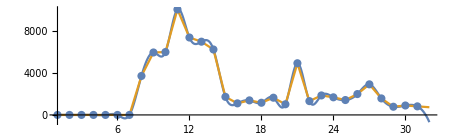

```mathematica
Show[Plot[{f[x],g[x]},{x,1,32},AspectRatio->.3],ListPlot[li⟦s;;-1,2⟧,Joined->False]]
```

### 通过样条插值增加10倍数据量

```mathematica
monthday=32;
```

```mathematica
lip=Table[Interpolation[li⟦s;;-1,y+1⟧, Method->"Spline"][x],{x,1,monthday+0.9,0.1},{y,col-1}];
Dimensions@lip
```

{320,346}

```mathematica
lip=ArrayFlatten[{{
Table[{li⟦Floor@j+s-1,1⟧},{j,1,monthday+0.9,0.1}],
lip
}}] ;
```

```mathematica
Export["lip2.csv",lip,CharacterEncoding-> "CP936"];
```